If[Abs[b]>Abs[a],If[v t≤Abs[a],t (b-a),If[v t≤Abs[b],(2 v b t-Abs[a] a-v^2 t^2)/(2 v),Abs[b] b-Abs[a] a]],If[v t≤Abs[b],t (b-a),If[v t≤Abs[a],(2 v b t-Abs[a] a-v^2 t^2)/(2 v),Abs[b] b-Abs[a] a]]]

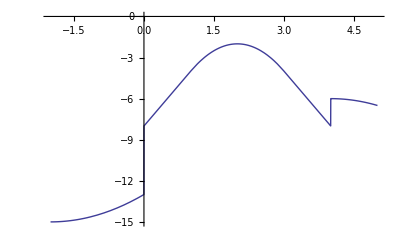

{1,2,3,4,5,0}

{-1.,-1.,-2.,-2.,-2.,-5.5}

```mathematica
u[x_, t_, a_, b_, v_] = 
If[Abs[b]>Abs[a],
If[v*t<=Abs[a], t*(b - a), 
If[v*t<=Abs[b], (2*v*b*t - Abs[a]*a-v^2*t^2)/2/v, 
(Abs[b]*(b)-Abs[a]*(a))]],
If[v*t<=Abs[b], t*(b - a), 
If[v*t<=Abs[a], (2*v*b*t - Abs[a]*a-v^2*t^2)/2/v, 
(Abs[b]*(b)-Abs[a]*(a))]]]
Plot[u[x,3,x-1,x-3,1], {x,-2,5}]
p={1,2,3,4,5,0}
Table[N[u[p[[i]],2,p[[i]]-1,p[[i]]-2,1]], {i, 1, Length[p]}]
```

1

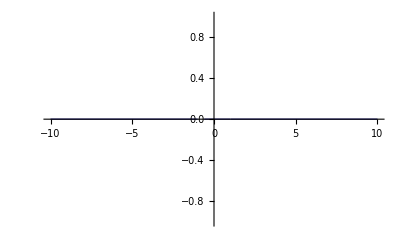

-2 HeavisideTheta[1-Abs[x]]-Sign[-1+x]+Sign[1+x]

0.

```mathematica
a = 1
Plot[{Sign[x + a] - Sign[x - a]- 2 *HeavisideTheta[Abs[a]-Abs[x]]*Sign[a]}, {x, -10, 10}]
null[x_, a_]=Sign[x + a] - Sign[x - a]- 2 *HeavisideTheta[Abs[a]-Abs[x]]*Sign[a]
N[null[0.5,3]]
```

```mathematica
u[x_, t_,v_, x0_,t0_] = -v/4*(Sign[(x-x0) + v*(t-t0)] - Sign[(x-x0) - v*(t-t0)])*HeavisideTheta[t-t0];
```

```mathematica
Plot[{u[x,3,1,0,0],u[x,2,1,0,0],u[x,1,1,0,0]},{x,-5,5},PlotStyle->{Thick,Thick,Thick},Filling->Axis, Ticks->{{{-3,"-3vΔt"},{-2,"-2vΔt"},{-1,"-vΔt"}, 0,{1,"vΔt"},{2,"2vΔt"},{3,"3vΔt"}},{{-1/2, "-v/2"}, 0}}]
```

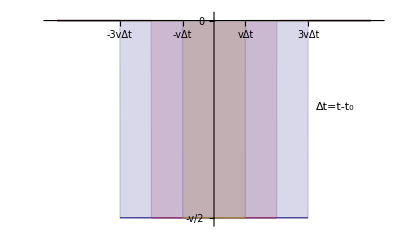

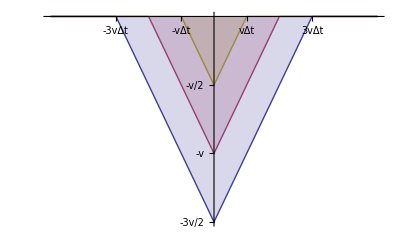

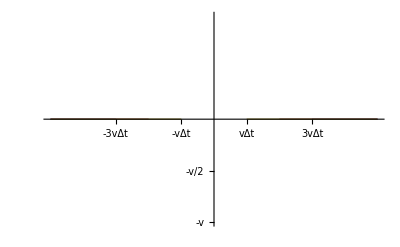

```mathematica
u2[x_, t_, v_, x0_, t0_] = - v/2*HeavisideTheta[t - t0]*HeavisideTheta[t -t0-Abs[x-x0]/v]*(t -t0-Abs[x-x0]/v);
Plot[{u2[x,3,1,0,0],u2[x,2,1,0,0],u2[x,1,1,0,0]},{x,-5,5},PlotStyle->{Thick,Thick,Thick},Filling->Axis, Ticks->{{{-3,"-3vΔt"},{-2,"-2vΔt"},{-1,"-vΔt"}, 0,{1,"vΔt"},{2,"2vΔt"},{3,"3vΔt"}},{{-1/2, "-v/2"}, {-1, "-v"},  {-3/2,"-3v/2"}}}]
du2[x_, t_, v_, x0_, t0_] = D[u2[x,t, v,x0,t0],{x,2}]-D[u2[x,t,v,x0,t0], {t,2}];
Plot[{du2[x,3,1,0,0],du2[x,2,1,0,0],du2[x,1,1,0,0]},{x,-5,5},PlotStyle->{Thick,Thick,Thick},Filling->Axis, Ticks->{{{-3,"-3vΔt"},{-2,"-2vΔt"},{-1,"-vΔt"}, 0,{1,"vΔt"},{2,"2vΔt"},{3,"3vΔt"}},{{-1/2, "-v/2"}, {-1, "-v"},  {-3/2,"-3v/2"}}}, ExclusionsStyle->Dashing[Small]]
```

-3.

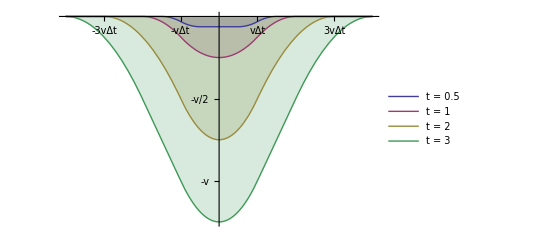

```mathematica
Sp[x_, xa_, xb_, xc_, yb_] =0.5*yb((x - xa)^2/(xb -xa)*HeavisideTheta[x- xa]*HeavisideTheta[xb-x]+
((xb-xa)+(2*xc-x-xb)/(xc -xb)*(x -xb))*HeavisideTheta[x- xb]*HeavisideTheta[xc-x]+
(xc-xa)*HeavisideTheta[x- xc]);
u3[x_, t_, v_, x0_, t0_, l_]=-v/2/l*(Sp[x+l/2,-v*(t -t0), 0, v*(t -t0), v*(t -t0)]-
Sp[x-l/2,-v*(t -t0), 0, v*(t -t0), v*(t -t0)]);
 Plot[{u3[x,0.5,1,0,0, 2],u3[x,1,1,0,0, 2],u3[x,2,1,0,0, 2],u3[x,3,1,0,0,2]},{x,-4,4},PlotStyle->{Thick,Thick,Thick},Filling->Axis, Ticks->{{{-3,"-3vΔt"},{-2,"-2vΔt"},{-1,"-vΔt"}, 0,{1,"vΔt"},{2,"2vΔt"},{3,"3vΔt"}},{{-1/2, "-v/2"}, {-1, "-v"},  {-3/2,"-3v/2"}}}, PlotLegends->{"t = 0.5", "t = 1", "t = 2","t = 3"}, Exclusions->None]
```

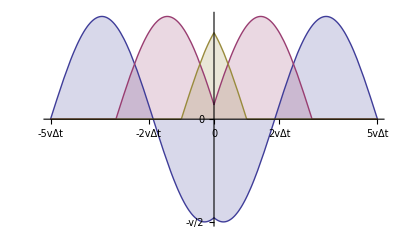

```mathematica
u4[x_, t_,v_, x0_,t0_,o_] = -v/4*(Sign[(x-x0) + v*(t-t0)] - Sign[(x-x0) - v*(t-t0)])*HeavisideTheta[t-t0]*(Sin[o*t0]-Sin[o*(t - Abs[x-x0]/v)]);
Plot[{u4[x,5,1,0,0,1],u4[x,3,1,0,0,1],u4[x,1,1,0,0,1]},{x,-5,5},PlotStyle->{Thick,Thick,Thick},Filling->Axis, Ticks->{{{-5,"-5vΔt"},{-3,"-3vΔt"},{-2,"-2vΔt"},{-1,"-vΔt"}, 0,{1,"vΔt"},{2,"2vΔt"},{3,"3vΔt"},{5,"5vΔt"}},{{-1/2, "-v/2"}, 0}}]
```